```mathematica
ydata=Map[ToExpression[#]&,Map[StringSplit[#,","]&,Import["/home/tm/Desktop/finance/NDAQ.csv","List"][[2;;]]][[;;,5]]];
```

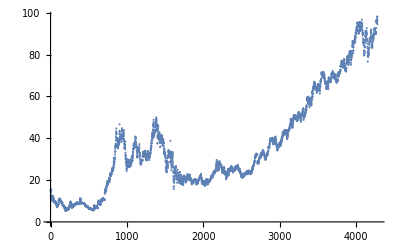

```mathematica
ListPlot@ydata
```

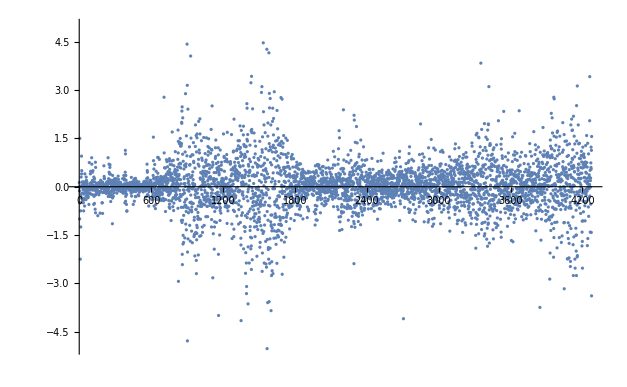

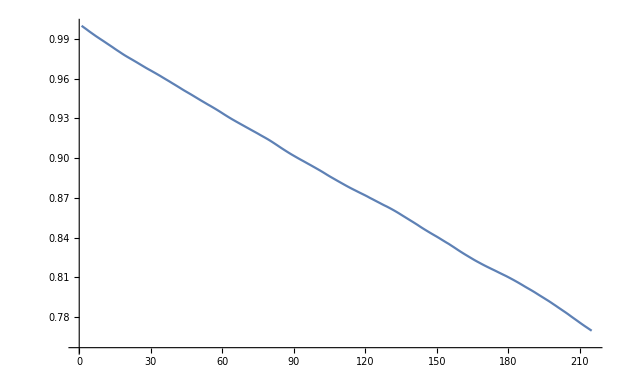

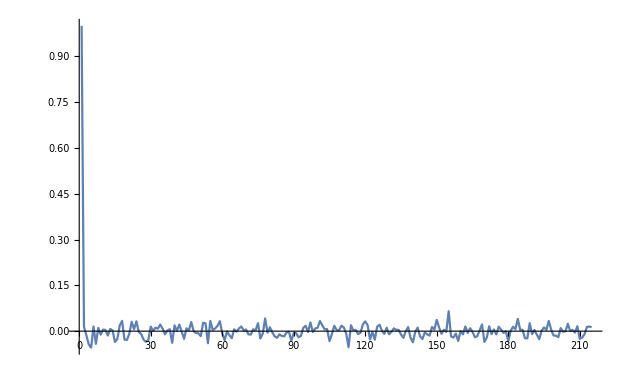

```mathematica
dydata=Differences@ydata;
ListPlot[dydata,PlotRange->{All,{-5,5}}]
ListLinePlot[CorrelationFunction[ydata,{0,Round[(Length@ydata)/20,1]}],PlotRange->All]
ListLinePlot[CorrelationFunction[dydata,{0,Round[(Length@ydata)/20,1]}],PlotRange->All]
```

```mathematica
n=Length@dydata;
```

```mathematica
distancematrixtmp=Table[Abs[dydata[[i]]-dydata[[j]]],{i,n},{j,n}];
max=Max[Flatten[distancematrixtmp]];
min=Min[Flatten[distancematrixtmp]];
distancematrix=(distancematrixtmp-min)/(max-min);
```

```mathematica
ArrayPlot[distancematrix]
```

-Graphics-

```mathematica
RescaledDistancematrix[distancematrix_]:=Module[{min,max,delta,list,res},
list=Flatten[distancematrix];
min=Min[list];
max=Max[list];
delta=max-min;
res=(distancematrix-min)/delta;
res
];
```

```mathematica
RecurrenceMatrix[distancematrix_,ϵ_/;0<ϵ<1,scale_/;scale]:=Map[HeavisideTheta[#-ϵ]&,RescaledDistancematrix@distancematrix,{2}];
RecurrenceMatrix[distancematrix_,ϵ_/;0<ϵ,scale_/;!scale]:=Map[HeavisideTheta[#-ϵ]&,distancematrix,{2}];
```

```mathematica
ListPlot[Sort[Flatten[distancematrix]]]
```

```mathematica
rm=RecurrenceMatrix[distancematrix,0.5,True];
```

```mathematica
ArrayPlot[rm]
```

-Graphics-